# Tubular segmentation inspired examples

## From the paper: Fast marching methods for curvature penalized shortest paths

This notebook is intended to reproduce the numerical experiments of the paper
J.-M. Mirebeau, Fast Marching Methods for curvature penalized shortest paths”, preprint available on HAL.

We mimick a common application of this method, which is the extraction of a tubular structure, amont
 an overlay of such structures. For that purpose, a minimal path, with respect to a data-dependent speed function and a well chosen curvature penalization, is extracted.
 
 Important note ! In real applications, the speed function should depend on the position AND the orientation. The choice here of a position dependent only speed function makes the problem harder on purpose, and the results worse than they should be, in order to exacerbate the differences between the different curvature penalization models.  

------------------ Usage -----------------
Please evaluate the notebook “Common.nb” first, and then this one.

The manipulate interfaces let you define the tubular structures, seeds and tips, parameters, which values are stored in the the following variables (Default values are those of the paper)
manCurve1Seg2; manCurve2Seg2; manSpeedPrmsSeg2;manSpeedSeg2; manTipsSeg2; 
Recall that Alt+Click lets you add a point, or delete an interactive point, in a manipulate interface.

Once these parameters are set, in another notebook, please evaluate one or several of the following lines, in Separate cells. The real number is the front propagation CPU time:
RunManSeg2[{“model”→”ReedsShepp2”,”xi”→#}]&/@{0.2,0.8}
RunManSeg2[{“model”→”ReedsSheppForward2”,”xi”→#}]&/@{0.2,0.8}
RunManSeg2[{“model”→”Elastica2<5>”,”xi”→#}]&/@{0.2,0.6,1.5} (*Good from 0.55 to 1.25*)
RunManSeg2[{“model”→”Dubins2”,”xi”→#}]&/@{0.2,0.35,0.5} (*Good from 0.25 to 0.38*)

```mathematica
execIso="FileHFM_AllBase";
execCurvature2="FileHFM_AllBase";
```

```mathematica
domainSeg2={{0,0},{1,1}};
rangeSeg2={#1-0.3,#2+0.3}&@@@Transpose@domainSeg2;
boxSeg2 = {Transparent,EdgeForm[Black],Rectangle@@domainSeg2};
imageSize=300;

DistToCurve[knots_,n_]:=Module[{fun=BSplineFunction[knots],pts,k=1,dist,params,refDir,out},
(*For now set for the unit square*)
Do[
pts=Table[fun[t],{t,0,1,1/(n 2^k)}];
dist=Norm/@(Drop[pts,1]-Drop[pts,-1]);
If[Max[dist≤1./n],Break[]];
,{k,1,7}];
pts=Map[Floor[n#]&,pts];
pts=Union[pts];
pts=Map[(#+0.5)/n&,pts];

params={ 
"dims"->{n,n},
"gridScale"->1./n,
"model"->"IsotropicBox2<Boundary::Closed>",
"seeds"->pts,
"exportValues"->1,
"progressReportLandmarks"->{},
"speed"->1
};
Return[RunExec[execIso,params]];
];

RasterCurve[{knots_,σ_},n_]:=Map[Exp[-#^2/(2σ^2)]&,"values"/.DistToCurve[knots,n],{2}];

SpeedCurves[curves_,n_]:=Module[{result=Array[1.&,{n,n}]},
Do[Module[{knots,sigma,speed},{knots,sigma,speed}=curve;
Print[RasterCurve[{knots,sigma},n]];
result=MapThread[Max[#1,speed #2]&,{result, RasterCurve[{knots,sigma},n]},2];
];,{curve,curves}];
result
];

RunSegmentation2[options_,params_]:=Module[{n=Length@manSpeedSeg2,opts,prms,out},
opts={"nDir"->60};opts=MergeRules[options,opts];
prms={
"dims"->{n,n,"nDir"/.opts},
"gridScale"->1./n,
"model"->"ReedsShepp2",
"speed"-> Map[Max[1.,#^2]&,manSpeedSeg2,{2}],
"progressReportLandmarks"->{},
"seeds"->manSeedsSeg2,
"tips"->manTipsSeg2,
"eps"->0.1,
"exportValues"->0
};
prms=MergeRules[params,prms];
{prms,RunExec[execCurvature2,prms]}
];

RunManSeg2[model_]:=Module[{prms,out,geo,h,tips,seeds,r=0.1},
{prms,out}=RunSegmentation2[{},model];
h="gridScale"/.prms;
geo="geodesics"/.out;
geo=Map[Drop[#,-1]&,geo,{2}];
tips={{#1,#2},{#1+r Cos[#3],#2+r Sin[#3]}}&@@@("tips"/.prms);
seeds={{#1,#2},{#1+r Cos[#3],#2+r Sin[#3]}}&@@@("seeds"/.prms);
{TablePlot[manSpeedSeg2,
{Epilog->{({Green,Line[#]}&/@(geo/h)),
{Blue,Point[First[#]]&/@(seeds/h),Arrow/@(seeds/h)},
{Red,Point[First[#]]&/@(tips/h),Arrow/@(tips/h)}
}}
],
"FMCPUTime"/.out}
];
```

```mathematica
{Manipulate[
manCurve1Seg2=pt;
Graphics[{boxSeg2,{Opacity[0.5],Red,BSplineCurve[manCurve2Seg2]},{Green,BSplineCurve[pt]},{Green,Line[pt]}},ImageSize->imageSize,PlotRange->rangeSeg2]
,{{pt,{{0.18,0.18},{0.55,0.05},{0.84,0.28},{0.65,0.51},{0.23,0.49},{0.2,0.78},
{0.38,0.94},{0.82,0.87},{0.84,0.69}}},Locator,LocatorAutoCreate->True}],
Manipulate[
manCurve2Seg2=pt;
Graphics[{boxSeg2,{Opacity[0.5],Green,BSplineCurve[manCurve1Seg2]},{Red,BSplineCurve[pt]},{GrayLevel[0.5],Line[pt]}},ImageSize->imageSize,PlotRange->rangeSeg2]
,{{pt,{{0.44,-0.01},{0.44,0.34},{0.62,0.68},{0.67,0.99}}},Locator,LocatorAutoCreate->True}]
}
```

{,}

```mathematica
(*SpeedCurves[{{manCurve1,0.03,4},{manCurve2,0.07,4}},100];*)
Manipulate[
manSpeedPrmsSeg2={σ1,s1,σ2,s2,Floor[Exp[n]]};
manSpeedSeg2=SpeedCurves[{{manCurve1Seg2,σ1,s1},{manCurve2Seg2,σ2,s2}},Floor[Exp[n]]];
TablePlot[manSpeedSeg2,{ImageSize->imageSize}]
,{{σ1,0.03},0,0.1},{{s1,4},1,10},{{σ2,0.07},0,0.1},{{s2,3},1,10},{{n,Log[73]},Log[10],Log[400]}]
```

```mathematica
{Manipulate[
manSeedsSeg2=Table[Append[pt[[2i-1]],Arg[(pt[[2i]]-pt[[2i-1]]).{1,I}]],{i,Floor[(Length@pt)/2]}];
ListDensityPlot[Transpose@manSpeedSeg2,DataRange->{{0,1},{0,1}},ImageSize->imageSize,
Epilog->(Arrow[{{#1,#2},{#1,#2}+0.15 {Cos[#3],Sin[#3]}}]&@@@manSeedsSeg2)]
,{{pt,{{0.16,0.17},{0.06,0.2},{0.49,0.06},{0.44,0.15}}},Locator,LocatorAutoCreate->True}],
Manipulate[
manTipsSeg2=Table[Append[pt[[2i-1]],Arg[(pt[[2i]]-pt[[2i-1]]).{1,I}]],{i,Floor[(Length@pt)/2]}];
ListDensityPlot[Transpose@manSpeedSeg2,DataRange->{{0,1},{0,1}},ImageSize->imageSize,
Epilog->(Arrow[{{#1,#2},{#1,#2}+0.15 {Cos[#3],Sin[#3]}}]&@@@manTipsSeg2)]
,{{pt,{{0.39,0.52},{0.48,0.5},{0.84,0.76},{0.8,0.85}}},Locator,LocatorAutoCreate->True}]
}
```

{,}

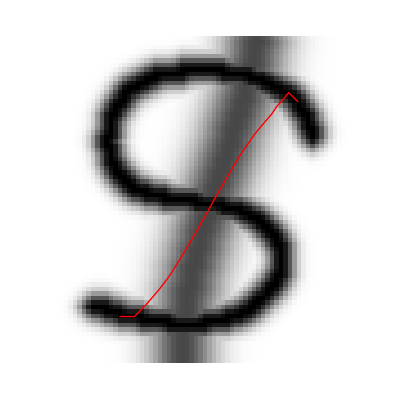

```mathematica
Module[{prms,out,geo,h},
{prms,out}=RunSegmentation2[{},{"model"->"ReedsSheppForward2","xi"->100}];
h="gridScale"/.prms;
geo="geodesics"/.out;
geo=Map[Drop[#,-1]/h&,geo,{2}];
TablePlot[manSpeedSeg2,{Epilog->({Red,Line[#]}&/@geo)}]]
```